```mathematica
mP=1.67*10^(-24); (*g*)
kB=1.38*10^(-16); (*in cgs*)
G=6.67*10^(-8);   (*in cgs*)
h=6.63*10^(-27); (*in cgs*)
Msun=1.989*10^33;
Rsun=6.9598*10^10;
Lsun=3.8418*10^33;
c=3*10^10;   (*cm/s*)
σSB=5.67*10^(-5); 
a=4*σSB/c;   
γ=5/3 ;
mu=0.62;
```

```mathematica
Polinomi=Table[q^i,{i,0,5}];
```

```mathematica
Model0=Import["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\AngularMomentumTransfer\\VariousModels\\SUN\\Model_Sun.dat","Table"];

Model=Drop[Model0,1];
```

```mathematica
RadiusMass=Model[[All,{6,5}]];
RadiusLogTemp=Model[[All,{6,3}]];
RadiusTemp=Table[{RadiusLogTemp[[i,1]],10^RadiusLogTemp[[i,2]]},{i,1,Dimensions[RadiusLogTemp][[1]]}];
RadiusLogDens=Model[[All,{6,4}]];
RadiusDens=Table[{RadiusLogDens[[i,1]],10^RadiusLogDens[[i,2]]},{i,1,Dimensions[RadiusLogDens][[1]]}];
RadiusLogPress=Model[[All,{6,2}]];
RadiusPress=Table[{RadiusLogPress[[i,1]],10^RadiusLogPress[[i,2]]},{i,1,Dimensions[RadiusLogPress][[1]]}];
RadiusLumin=Model[[All,{6,7}]];
RadiusOpacity=Model[[All,{6,9}]];
RadiusGrav=Table[{RadiusMass[[i,1]], (G*RadiusMass[[i,2]])/RadiusMass[[i,1]]^2},{i,1,Dimensions[RadiusMass][[1]]}];
```

```mathematica
RhoN=Interpolation[RadiusDens];
PN=Interpolation[RadiusPress];
TN=Interpolation[RadiusTemp];
Grav=Interpolation[RadiusGrav];
OpacityN=Interpolation[RadiusOpacity];
```

```mathematica
Rtot=Model[[1,6]]/Model[[1,16]];

RDown=69*10^-2*Rtot;
RUp=71*10^-2*Rtot;
```

```mathematica
RadiusGravReduced=Select[RadiusGrav,RDown<#[[1]]<RUp&];
RadiusTempReduced=Select[RadiusTemp,RDown<#[[1]]<RUp&];
RadiusPressReduced=Select[RadiusPress,RDown<#[[1]]<RUp&];
RadiusDensReduced=Select[RadiusDens,RDown<#[[1]]<RUp&];
RadiusOpacityReduced=Select[RadiusOpacity,RDown<#[[1]]<RUp&];
```

```mathematica
RhoFit0=Fit[RadiusDensReduced,Polinomi,q];
RhoFit[x_]=RhoFit0/.{q->x};
Show[Plot[RhoN[r],{r,RDown,RUp}],ListPlot[RadiusDensReduced],Plot[RhoFit[r],{r,RDown,RUp},PlotStyle->Green],Frame->True,FrameLabel->{"r (cm)","rho (g/cm^3)","Density"},BaseStyle->{FontWeight->"Bold",FontSize->16},Axes->None];
ρ[R_,z_]=RhoFit[(R^2+z^2)^0.5];
```

```mathematica
TempFit0=Fit[RadiusTempReduced,Polinomi,q];
TempFit[x_]=TempFit0/.{q->x};
Show[Plot[TN[r],{r,RDown,RUp}],ListPlot[RadiusTempReduced],Plot[TempFit[r],{r,RDown,RUp},PlotStyle->Green],Frame->True,FrameLabel->{"r (cm)","T (K)","Temperature"},BaseStyle->{FontWeight->"Bold",FontSize->16},Axes->None];
T[R_,z_]=TempFit[(R^2+z^2)^0.5];
```

```mathematica
PressFit0=Fit[RadiusPressReduced,Polinomi,q];
PressFit[x_]=PressFit0/.{q->x};
Show[Plot[PN[r],{r,RDown,RUp}],ListPlot[RadiusPressReduced],Plot[PressFit[r],{r,RDown,RUp},PlotStyle->Green],Frame->True,FrameLabel->{"r (cm)","P (g/(cm*s^2))","Pressure"},BaseStyle->{FontWeight->"Bold",FontSize->16},Axes->None];
P[R_,z_]=PressFit[(R^2+z^2)^0.5];
PdR[R_,z_]=D[P[R,z],R];   Pdz[R_,z_]=D[P[R,z],z];
dLogPdLogr[R_,z_]=(P[R,z]/(√(R^2+z^2)))^-1*PressFit'[√(R^2+z^2)];
SoundSpeed[R_,z_]=√(γ P[R,z] / ρ[R,z]);
```

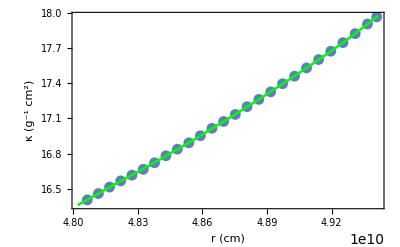

```mathematica
κFit0=Fit[RadiusOpacityReduced,Polinomi,q];
κFit[x_]=κFit0/.{q->x};
Show[Plot[OpacityN[r],{r,RDown,RUp}],ListPlot[RadiusOpacityReduced],Plot[κFit[r],{r,RDown,RUp},PlotStyle->Green],Frame->True,FrameLabel->{"r (cm)","κ (g^-1 cm^2)","Opacity"},BaseStyle->{FontWeight->"Bold",FontSize->16},Axes->None]
κ[R_,z_]=κFit[(R^2+z^2)^0.5];
```

```mathematica
σ[R_,z_]=Log[P[R,z]*ρ[R,z]^(-γ)];
σdR[R_,z_]=D[σ[R,z],R];
σdz[R_,z_]=D[σ[R,z],z];
σdr[R_,z_]=σdR[R,z]*R/(√(R^2+z^2))+σdz[R,z]*z/(√(R^2+z^2));
σdLogr[R_,z_]=√(R^2+z^2)*σdr[R,z];
```

```mathematica
Mu=0.62;
χ[R_,z_]=(16*T[R,z]^3*σSB*(γ-1)*Mu*mP)/(3*κ[R,z]*ρ[R,z]^2*kB);   (*this is what Goldreich and Schubert call χ*)
Λ=10^4;    νdyn[R_,z_]=2.2*10^-15*T[R,z]^(5/2)/(ρ[R,z]*Log10[Λ]);   (*dynamic viscosity by Spitzer*)

 νrad[R_,z_]=16/15*(σSB*T[R,z]^4)/(κ[R,z]*ρ[R,z]^2*c^2);   (*radiative viscosity by Menou and Balbus*)
ν[R_,z_]=νrad[R,z]+νdyn[R,z];
Pr[R_,z_]=ν[R,z]/χ[R,z];
```

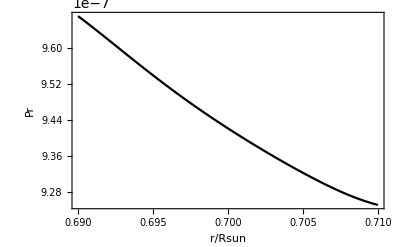

```mathematica
Plotχ=Plot[χ[r*Rsun*Sin[π/4],r*Rsun*Cos[π/4]],{r,RDown/Rsun,RUp/Rsun},Frame->True,FrameLabel->{"r/Rsun","χ (cm^2 s^-1)"},BaseStyle->{FontWeight->"Bold",FontSize->12},PlotStyle->Black];
Show[LogPlot[ν[r*Rsun*Sin[π/4],r*Rsun*Cos[π/4]],{r,RDown/Rsun,RUp/Rsun},PlotStyle->Directive[Black],PlotRange->{{RDown/Rsun,RUp/Rsun},{0.1,1000}}],LogPlot[νdyn[r*Rsun*Sin[π/4],r*Rsun*Cos[π/4]],{r,RDown/Rsun,RUp/Rsun},PlotStyle->Directive[Black,Dashed],PlotRange->{{RDown/Rsun,RUp/Rsun},{0.1,1000}}],LogPlot[νrad[r*Rsun*Sin[π/4],r*Rsun*Cos[π/4]],{r,RDown/Rsun,RUp/Rsun},PlotStyle->Directive[Black,Dotted],PlotRange->{{RDown/Rsun,RUp/Rsun},{0.1,1000}}],Frame->True,FrameLabel->{"r/Rsun","ν (cm^2 s^-1)"},BaseStyle->{FontWeight->"Bold",FontSize->12}];
PlotPr=Plot[Pr[r*Rsun*Sin[π/4],r*Rsun*Cos[π/4]],{r,RDown/Rsun,RUp/Rsun},Frame->True,FrameLabel->{"r/Rsun","Pr"},BaseStyle->{FontWeight->"Bold",FontSize->12},PlotStyle->Black]
```

```mathematica
Ω[R_,z_]:=√(7.4*10^-12);      dLogΩdLogr:=-1.1;
ldR[R_,z_]:=Ω[R,z]*R*(2+R^2/(R^2+z^2)*dLogΩdLogr);   ldz[R_,z_]:=Ω[R,z]*R*(z/(√(R^2+z^2))*dLogΩdLogr);
LastTermGS[R_,z_,kR_,kz_]:=(kz^2/(kR^2+kz^2))*1/(γ*Ω[R,z]^2 ρ[R,z])*((ν[R,z]*(kR^2+kz^2))/Ω[R,z])(PdR[R,z]-kR/kz Pdz[R,z])(kR/kz σdz[R,z]-σdR[R,z])+(2/(γ*Ω[R,z]*R))(kz^2/(kR^2+kz^2))((χ[R,z]*(kR^2+kz^2))/Ω[R,z])(ldR[R,z]-kR/kz ldz[R,z])+1/γ((χ[R,z]*(kR^2+kz^2))/Ω[R,z])((ν[R,z]*(kR^2+kz^2))/Ω[R,z])^2
```

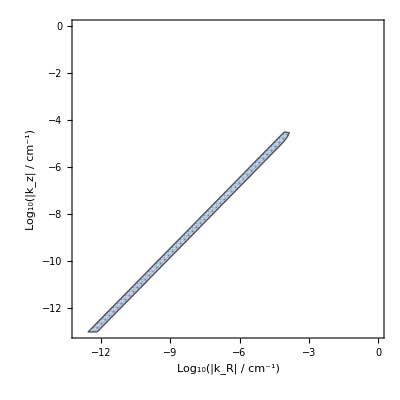
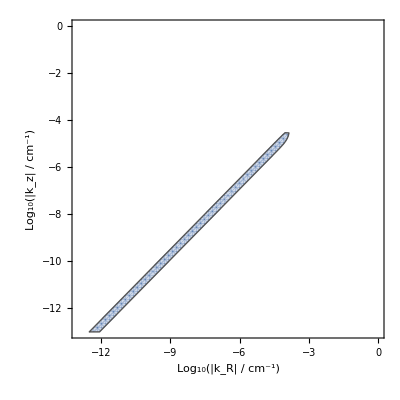
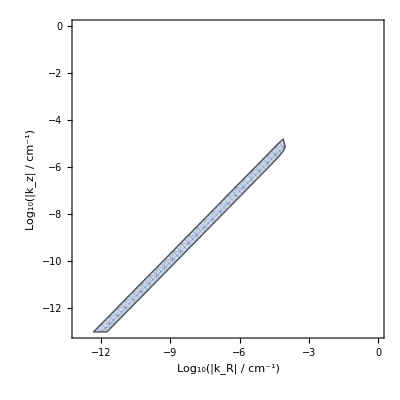
{3.67188,{-Graphics- -Graphics-,-Graphics- -Graphics-,-Graphics- -Graphics-}}

```mathematica
rper = (RDown+RUp)/2;

Timing[Table[
Rper=rper*Sin[θper];   zper=rper*Cos[θper];

RegionPlot[LastTermGS[Rper,zper,10^LogKappaR,10^LogKappaz]<0,{LogKappaR,-13,0},{LogKappaz,-13,0},FrameLabel->{"Log_10(|k_R| / cm^-1)","Log_10(|k_z| / cm^-1)","k_R > 0, k_z > 0"},BaseStyle->{FontWeight->"Bold",FontSize->8}]
RegionPlot[LastTermGS[Rper,zper,-10^LogKappaR,10^LogKappaz]<0,{LogKappaR,-13,0},{LogKappaz,-13,0},FrameLabel->{"Log_10(|k_R| / cm^-1)","Log_10(|k_z| / cm^-1)","k_R < 0, k_z > 0"},LabelStyle->Black,BoundaryStyle->{Darker[Gray],Thick},BaseStyle->{FontWeight->"Bold",FontSize->8}]
,{θper,π/36*4,14*π/36,5*π/36}]]
```

```mathematica
(*RadiusMinShear={{(RUp+RDown)/2,6.5}}*)
```

```mathematica
RadiusMinShear=Append[RadiusMinShear,{(RUp+RDown)/2,1.1}]
```

{{1.73995×10^9,6.5},{2.43593×10^9,8},{2.78392×10^9,8},{3.13191×10^9,8.5},{3.82789×10^9,10},{1.04397×10^9,0},{1.11357×10^9,2.5},{3.82789×10^9,10},{4.87186×10^9,10},{5.91583×10^9,10},{6.9598×10^9,10},{9.04775×10^9,10},{1.11357×10^10,9.5},{1.39196×10^10,9},{1.80955×10^10,7.5},{2.01834×10^10,7},{2.29674×10^10,6},{2.57513×10^10,5},{2.85352×10^10,4.5},{3.13191×10^10,3.5},{3.4103×10^10,3},{3.6191×10^10,3},{3.89749×10^10,2.5},{4.17588×10^10,2},{4.31508×10^10,1.6},{4.38468×10^10,1.5},{4.45428×10^10,1.5},{4.52387×10^10,1.4},{4.59347×10^10,1.3},{4.66307×10^10,1.3},{4.73267×10^10,1.2},{4.80227×10^10,1.1},{4.87186×10^10,1.1}}

```mathematica
RadiusMinShear=Drop[RadiusMinShear,-1]
```

{{1.73995×10^9,6.5},{2.43593×10^9,8},{2.78392×10^9,8},{3.13191×10^9,8.5},{3.82789×10^9,10},{1.04397×10^9,0},{1.11357×10^9,2.5},{3.82789×10^9,10},{4.87186×10^9,10},{5.91583×10^9,10},{6.9598×10^9,10},{9.04775×10^9,10},{1.11357×10^10,9.5},{1.39196×10^10,9},{1.80955×10^10,7.5},{2.01834×10^10,7},{2.29674×10^10,6},{2.57513×10^10,5},{2.85352×10^10,4.5},{3.13191×10^10,3.5},{3.4103×10^10,3},{3.6191×10^10,3},{3.89749×10^10,2.5},{4.17588×10^10,2},{4.31508×10^10,1.6},{4.38468×10^10,1.5},{4.45428×10^10,1.5},{4.52387×10^10,1.4},{4.59347×10^10,1.3},{4.66307×10^10,1.3},{4.73267×10^10,1.2},{4.80227×10^10,1.1}}

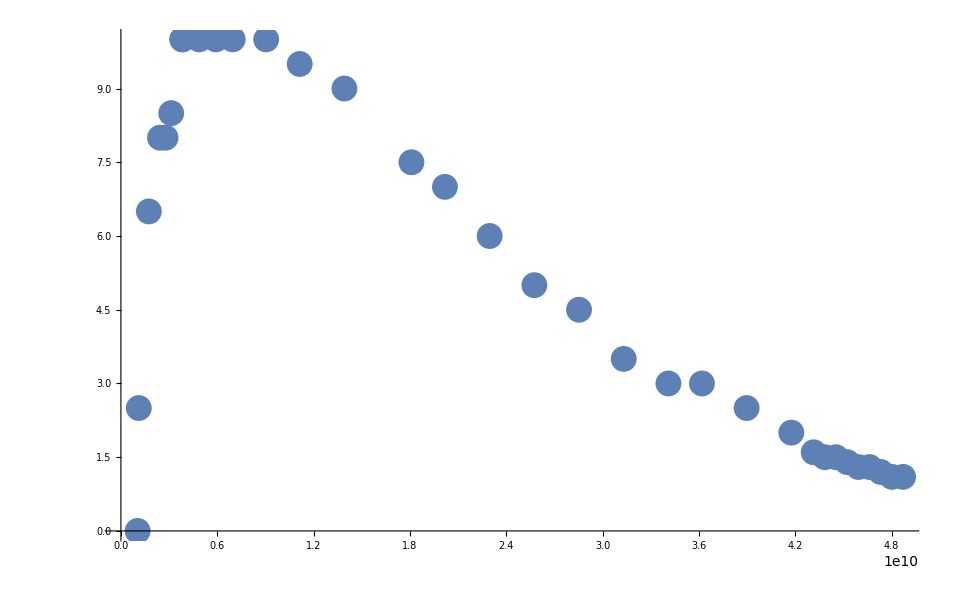

```mathematica
ListPlot[RadiusMinShear]
```

```mathematica
RadiusMinShearFinal={{1.73995*10^9,6.5},{2.43593*10^9,8},{2.78392*10^9,8},{3.13191*10^9,8.5},{3.82789*10^9,10},{1.04397*10^9,0},{1.11357*10^9,2.5},{4.87186*10^9,10},{5.91583*10^9,10},{6.9598*10^9,10},{9.04775*10^9,10},{1.11357*10^10,9.5},{1.39196*10^10,9},{1.80955*10^10,7.5},{2.01834*10^10,7},{2.29674*10^10,6},{2.57513*10^10,5},{2.85352*10^10,4.5},{3.13191*10^10,3.5},{3.4103*10^10,3},{3.6191*10^10,2.75},{3.89749*10^10,2.5},{4.17588*10^10,2},{4.31508*10^10,1.6},{4.38468*10^10,1.5},{4.45428*10^10,1.5},{4.52387*10^10,1.4},{4.59347*10^10,1.3},{4.66307*10^10,1.3},{4.73267*10^10,1.2},{4.80227*10^10,1.1},{4.87186*10^10,1.1}};
```

{{1.73995×10^9,6.5},{2.43593×10^9,8},{2.78392×10^9,8},{3.13191×10^9,8.5},{3.82789×10^9,10},{1.04397×10^9,0},{1.11357×10^9,2.5},{4.87186×10^9,10},{5.91583×10^9,10},{6.9598×10^9,10},{9.04775×10^9,10},{1.11357×10^10,9.5},{1.39196×10^10,9},{1.80955×10^10,7.5},{2.01834×10^10,7},{2.29674×10^10,6},{2.57513×10^10,5},{2.85352×10^10,4.5},{3.13191×10^10,3.5},{3.4103×10^10,3},{3.6191×10^10,2.75},{3.89749×10^10,2.5},{4.17588×10^10,2},{4.31508×10^10,1.6},{4.38468×10^10,1.5},{4.45428×10^10,1.5},{4.52387×10^10,1.4},{4.59347×10^10,1.3},{4.66307×10^10,1.3},{4.73267×10^10,1.2},{4.80227×10^10,1.1},{4.87186×10^10,1.1}}

9            10
InterpolatingFunction[{{1.04397 10 , 4.87186 10  }}, <>]

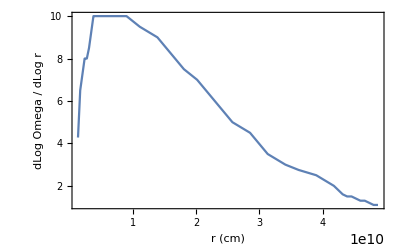

InterpolatingFunction::dmval: Input value {6.96961×10^8} lies outside the range of data in the interpolating function. Extrapolation will be used.

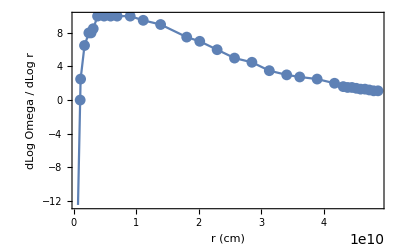

```mathematica
RadiusMinShear2=RadiusMinShearFinal
MinShearN=Interpolation[RadiusMinShear2,InterpolationOrder->1]
Plot[MinShearN[r],{r,0.02Rsun,0.7Rsun},PlotRange->Full,Frame->True,FrameLabel->{"r (cm)","dLog Omega / dLog r"},BaseStyle->{FontWeight->"Bold",FontSize->16}]
Show[Plot[MinShearN[r],{r,0.01Rsun,0.7Rsun},PlotRange->Full],ListPlot[RadiusMinShearFinal],Frame->True,FrameLabel->{"r (cm)","dLog Omega / dLog r"},BaseStyle->{FontWeight->"Bold",FontSize->16},Axes->None]
```

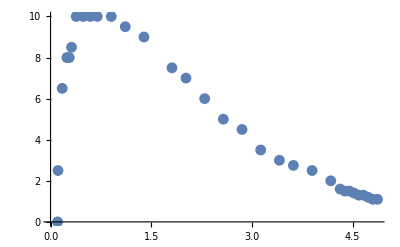

```mathematica
ListPlot[RadiusMinShearFinal]
```